```mathematica
data=Flatten[Import["/home/drladiges/projects/FHDeX/exec/immersedIons/conductivityEst","CSV"]][[1;;-1]];
p1=ListPlot[data]
Length[data]
```

-Graphics-

1031745

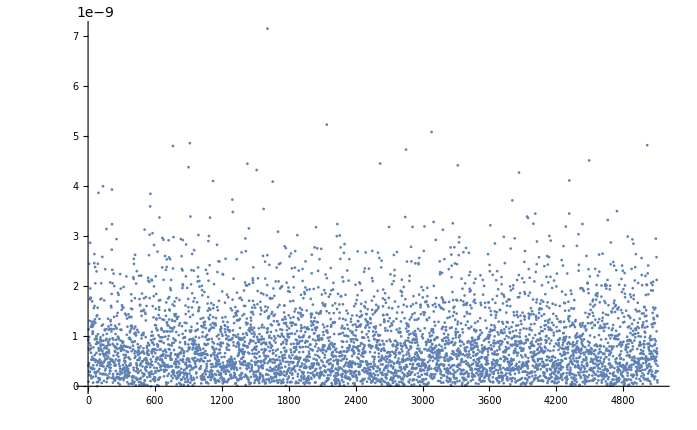

5109

```mathematica
nn=200;
skip=10000;
testL=Length[data];
cond=Table[data[[ii-1]],{ii,skip,Length[data],nn}];
ListPlot[cond,PlotRange->All]
samples=Length[cond]
```

```mathematica
StandardDeviation[cond]
StandardDeviation[cond]/(samples^(1/2))
Mean[cond]
```

6.91092×10^-10

9.6687×10^-12

8.41953×10^-10

```mathematica
testL=samples-1;
msd=Table[0,{ii,1,testL}];
For[i=0,i<testL,i++,
run=data[[skip+i*nn+1;;skip+(i+1)*nn]];
msd[[i+1]]=run;
];
msdMean=Mean[msd];
```

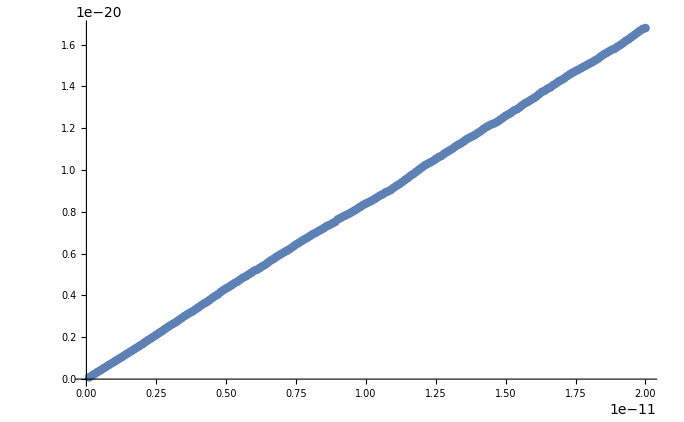

```mathematica
msdTime =Table[0,{ii,1,nn}];
dt=10^-13;
For[i=1,i≤nn,i++,
msdTime[[i]]={i dt,msdMean[[i]]*i dt};
];

ListPlot[msdTime,AxesOrigin->{0,0}]
```

```mathematica
NotebookDirectory[]
```

/home/drladiges/projects/FHDeX/exec/immersedIons/